```mathematica
(*Initial Conditions for the system*)
```

```mathematica
Manipulate[Plot3D[{k*x(x-1.5)(x-3)y(y-1),5},{x,0,3},{y,0,1}],{k,-20,10}]
```

```mathematica
(*See what happens when boundary conditions are only the border*)
```

```mathematica
alpha3 = 0.05; kk = -20;
vvalsNoRod = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[3,y,t]==0}},v,{x,0,3},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 3.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot3D[{vvalsNoRod[x,y,t],6.5,-6.5},{x,0,3},{y,0,1}],{t,0,10}]
```

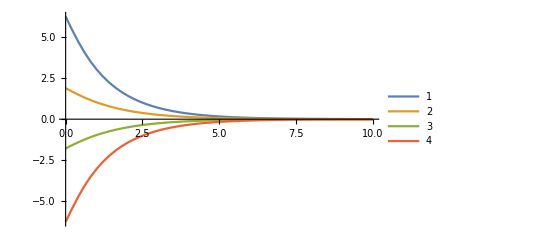

```mathematica
Plot[{vvalsNoRod[0.5,0.5,t],vvalsNoRod[1.33,0.5,t],vvalsNoRod[1.66,0.5,t],vvalsNoRod[2.5,0.5,t]},{t,0,10},PlotLegends -> Automatic, PlotRange->All]
```

```mathematica
(*This is the first rod*)
```

```mathematica
alpha1 = 0.12; 
uvals1 = NDSolveValue[{{D[u[y,t],t]==alpha1*D[u[y,t],{y,2}]},{u[y,0]==kk*y(y-1)},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot[{uvals1[y,t],vvalsNoRod[1,y,t],5},{y,0,1},PlotLegends -> Automatic],{t,0,10}]
```

```mathematica
(*This is the second rod*)
```

```mathematica
uvals2= NDSolveValue[{{D[u[y,t],t]==alpha1*D[u[y,t],{y,2}]},{u[y,0]==-kk*y(y-1)},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 20.}}, <>]

```mathematica
Manipulate[Plot[{uvals2[y,t],vvalsNoRod[2,y,t],-5},{y,0,1},PlotLegends -> Automatic],{t,0,10}]
```

```mathematica
(*This is solving the region with rod 1 as the right boundary*)
```

```mathematica
vvalsRod1 = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[1,y,t]==uvals1[y,t]}},v,{x,0,1},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is solving the region with rod 2 as the right boundary*)
```

```mathematica
vvalsRod2 = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[2,y,t]==uvals2[y,t]},{v[1,y,t]==uvals1[y,t]}},v,{x,1,2},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{1., 2.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is solving the region with rod 2 as the left boundary*)
```

```mathematica
vvalsRod3 = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[3,y,t]==0},{v[2,y,t]==uvals2[y,t]}},v,{x,2,3},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{2., 3.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*Now we plot the points*)
```

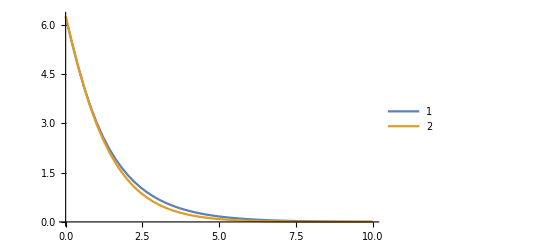

```mathematica
Plot[{vvalsNoRod[0.5,0.5,t],vvalsRod1[0.5,0.5,t]},{t,0,10},PlotLegends -> Automatic, PlotRange->All]
```

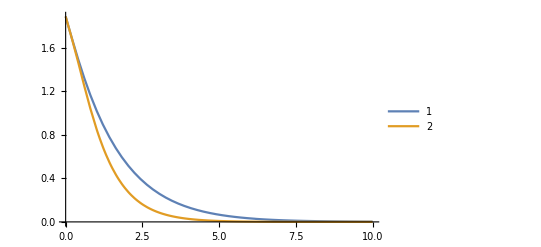

```mathematica
Plot[{vvalsNoRod[1.33,0.5,t],vvalsRod2[1.33,0.5,t]},{t,0,10},PlotLegends -> Automatic, PlotRange->All]
```

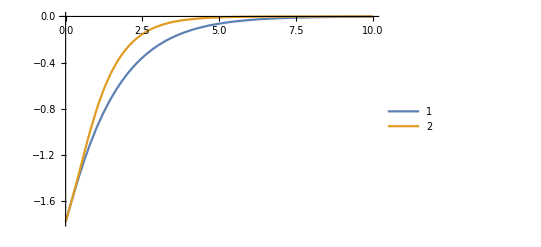

```mathematica
Plot[{vvalsNoRod[1.66,0.5,t],vvalsRod2[1.66,0.5,t]},{t,0,10},PlotLegends -> Automatic, PlotRange->All]
```

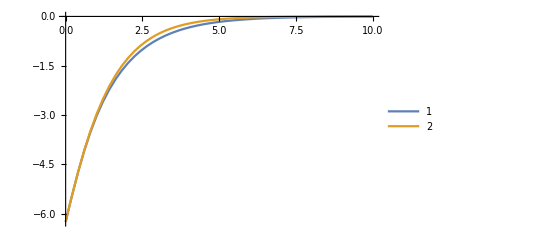

```mathematica
Plot[{vvalsNoRod[2.5,0.5,t],vvalsRod3[2.5,0.5,t]},{t,0,10},PlotLegends -> Automatic, PlotRange->All]
```